```mathematica
1+1
```

2

```mathematica
om = 0.3;
w0linear = -1.25;
w1linear = 1.97;
w0linder=-1.29;
w1linder= 2.84;
a1 = -3.36;
a2= 2.12;
a3 = -0.06 Pi;
```

```mathematica
elcdmA[a_]=√(om/a^3+1-om);
```

```mathematica
slcdm = NDSolve[{d''[a] + (3/a + elcdmA'[a]/elcdmA[a])d'[a] - 3/2 om / (a^5 elcdmA[a]^2) d[a] == 0, d[0.01]== 0.0001, d'[0.01]==0.01}, d, {a, 0.01, 1}];
```

```mathematica
deltalcdm[a_]:=d[a]/.Flatten[slcdm]
```

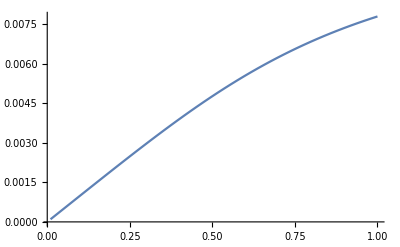

```mathematica
plotdeltalcdm=Plot[deltalcdm[a],{a,0.01,1}]
```

```mathematica
flcdm[a_]:=(deltalcdm'[a]*a)/deltalcdm[a]
```

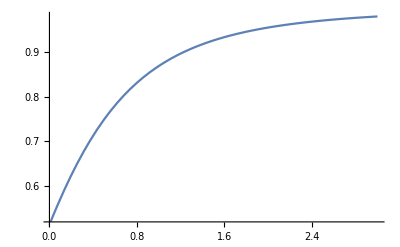

```mathematica
plotflcdm=Plot[flcdm[1/(1+z)],{z,0.01,3}]
```

```mathematica
omegam[a_,e_]:=om/(a^3 e[a]^2)
```

```mathematica
gammalcdm[a_]:=Log[flcdm[a]]/Log[omegam[a,elcdmA]]
```

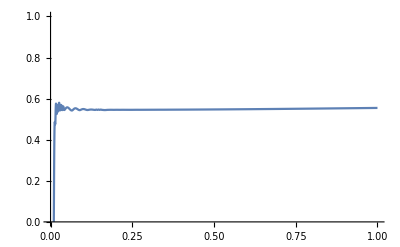

```mathematica
Plot[gammalcdm[a],{a,0.01,1}, PlotRange->{0,1}]
```

```mathematica
eode[a_] = Sqrt[om (1/a)^3 + a1 Cos[a2 (1/a-1)^2 + a3] + (1 - a1 Cos[a3] - om)];
```

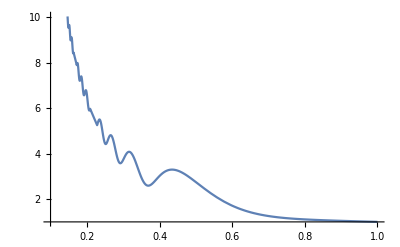

```mathematica
Plot[eode[a],{a,0.1,1}]
```

```mathematica
sode = NDSolve[{d''[a] + (3/a + eode'[a]/eode[a])d'[a] - 3/2 om / (a^5 eode[a]^2) d[a] == 0, d[0.01]== 0.0001, d'[0.01]==0.01}, d, {a, 0.01, 1}];
```

```mathematica
deltaode[a_]:=d[a]/.Flatten[sode]
```

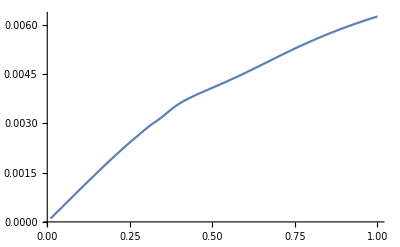

```mathematica
plotdeltaode=Plot[deltaode[a],{a,0.01,1}]
```

```mathematica
fode[a_]:=(deltaode'[a]*a)/deltaode[a]
```

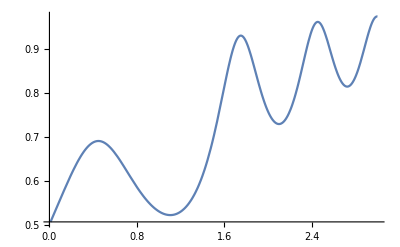

```mathematica
plotfode=Plot[fode[1/(1+z)],{z,0.01,3}]
```

```mathematica
gammaode[a_]:=Log[fode[a]]/Log[omegam[a,eode]]
```

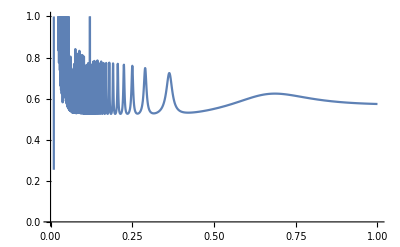

```mathematica
Plot[gammaode[a],{a,0.01,1}, PlotRange->{0,1}]
```